```mathematica
Quit[];
```

```mathematica
Import["/Users/conordyson/Documents/GitHub/BHPT/KerrGeodesics/KerrGeodesicsTest/Kernel/KerrGeoPlunge.m"]
```

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
PacletDirectoryLoad["."];
```

```mathematica
<<KerrGeodesics`
```

```mathematica
<<MaTeX`
```

```mathematica
textStyle = {FontFamily->"Times New Roman",FontSize->14}
```

{FontFamily→Times New Roman,FontSize→14}

## ISSO Testing

```mathematica
a =0.95;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
θ0 = π/3;
orbit = KerrGeoPlunge[a, "ISSORadialParam",8,{0,4,-π/2.2,0}]
R1 = orbit["RadialRoots"][[1]];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];
{t[0],r[0],θ[0],ϕ[0]}
```

KerrGeoPlungeFunction[…]

{-1.42109×10^-14,4.,1.428,4.44089×10^-16}

```mathematica
N[ArcCos[π/2]]
```

0.+1.02323 ⅈ

```mathematica
orbit["ConstantsOfMotion"]
```

<|ℰ→0.923305,ℒ→0.862706,𝒬→8.55805|>

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,-20,0}, MaxRecursion->10, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### ISSO Paper Plots

```mathematica
v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ+0.0001*I]]],Re[r[λ]]Cos[Re[ϕ[λ+0.0001*I]]]}, {λ,-20,0},ImageSize->300, PlotRange->All,PlotLabel->MaTeX["\\text{Projection onto Co-Precessing plane}", FontSize->14], PlotStyle->Red, MaxRecursion->14,Frame->True,FrameStyle->Directive[ColorData[112][6],14],FrameLabel->{  MaTeX["r\\sin{\\phi}",FontSize->14], MaTeX["r\\cos{\\phi}",FontSize->14]},Prolog->{ColorData[112][6], Opacity[0.0],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];

v2 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,PlotRange->All,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotLegends->{MaTeX["r_I",FontSize->14], MaTeX["r_+",FontSize->14], MaTeX["r_-",FontSize->14],MaTeX["r_4",FontSize->14]}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{r[λ]*Sin[θ[λ]],r[λ]*Cos[θ[λ]]} , {λ,-20,0},ImageSize->300, PlotRange->All,PlotLabel->MaTeX[ "\\text{Projection onto Co-Rotating plane}",FontSize->14],MaxRecursion->12,FrameTicks->{{None,All},{All,None}}
,FrameStyle->Directive[ColorData[112][3],14], PlotStyle->Red,Frame->True,FrameStyle->Center,FrameLabel->{{None,MaTeX["r\\sin\\theta",FontSize->14]},{ MaTeX["r\\cos\\theta",FontSize->14],None}},Prolog->{ColorData[112][3], Opacity[0],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];

Q2 = ParametricPlot[{{RI*Cos[π/2-u],RI Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{R4*Cos[π/2-u],R4 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,Frame->True,FrameStyle->Center,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];
corotatingISSOPlots = Row[{a1,a2}]
Export["corotatingISSOPlots.pdf",Style[corotatingISSOPlots,LineBreakWithin->False],"PDF"]
```

-Graphics--Graphics-

corotatingISSOPlots.pdf

```mathematica
λ0 = -13.9;
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,-20,0}, PlotLabel-> MaTeX["\\text{3D Spatial Plot}",FontSize->14],ImageSize->400,MaxRecursion->10, PlotStyle->Red,PlotRange->All , AxesLabel->{MaTeX["r\\sin{\\phi}\\sin{\\theta}",FontSize->14],MaTeX["r\\sin{\\theta}\\cos{\\phi}",FontSize->14],MaTeX["r\\cos{\\theta}",FontSize->14]}, LabelingSize->30];


P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];

P3 = Graphics3D[{Black,Opacity[1], Specularity[White,10],Sphere[path[λ0],0.1]}];

P4 = ParametricPlot3D[{u Cos[ϕ[λ0]]+v Sin[θ[λ0]] Sin[ϕ[λ0]],v Cos[ϕ[λ0]] Sin[θ[λ0]]-u Sin[ϕ[λ0]],v Cos[θ[λ0]]},{u,-RI-0.1,RI+0.1},{v,-RI-0.1,RI+0.1},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[0.4],ColorData[112][6],Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All,Mesh->10];


P5 = ParametricPlot3D[{u Sin[ϕ[λ0]], u Cos[ϕ[λ0]] ,v },{u,-RI-m,RI+m},{v,-RI-m,RI+m},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[0.4],ColorData[112][3],Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All,Mesh->10];
a1 = Show[P1,P2,P3,P4,P5];
ISSOPlots =a1
Export["ISSOPlots.pdf",Style[ISSOPlots,LineBreakWithin->False],"PDF"]
```

-Graphics3D-

ISSOPlots.pdf

ISSOPlots.pdf

```mathematica
Export["ISSOPlots.pdf",-Graphics3D-,"PDF"]
```

ISSOPlots.pdf

```mathematica
Export["ISSOPlots.pdf",-Graphics3D-,"PDF"]
```

ISSOPlots.pdf

```mathematica
Clear[Z1,Z2,z]
```

```mathematica
Solve[z== Z1*JacobiSN[Z2*λ ,kz^2],λ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## Generic Testing

```mathematica
(*a =0.9;
ϵ = 0.9568977877615272;
L = 2.5513895720207542;
Q =6.5437491308459705;
ϵ = 0.9;
L = 2;
Q =6;*)
```

### Setting Up Generic

```mathematica
a =0.9;
ϵ = 0.956`5;
L = 2.551`5;
Q =6.543`5;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a,{ϵ,L,Q},{4,1,2, 6}];
orbit["RadialRoots"];
{r1,r2} = TakeSmallest[Select[orbit["RadialRoots"],Im[#]==0&],2];
{Z1,Z2}=orbit["PolarRoots"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
{t,r,θ,ϕ} = orbit["Trajectory"];
z[λ_]:= Cos[θ[λ]];
r1
{t[0],r[0],θ[0],ϕ[0]}
```

0.374006

{4.-8.88178×10^-16 ⅈ,1.+0. ⅈ,1.99994,6.+0. ⅈ}

```mathematica
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,0,2},ImageSize->400,MaxRecursion->10, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->12,PlotStyle->{Opacity[0],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### Generic Plots

```mathematica
v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ+0.0001*I]]],Re[r[λ]]Cos[Re[ϕ[λ+0.0001*I]]]}, {λ,-10,0},ImageSize->300, PlotRange->All,PlotLabel->MaTeX["\\text{Projection onto Co-Precessing plane}", FontSize->14], PlotStyle->Red, MaxRecursion->14,Frame->True,FrameStyle->Directive[ColorData[112][6],14],FrameLabel->{  MaTeX["r\\sin{\\phi}",FontSize->14], MaTeX["r\\cos{\\phi}",FontSize->14]},Prolog->{ColorData[112][6], Opacity[0.0],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];

v2 = ParametricPlot[{{r2*Cos[u],r2 Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{r1*Cos[u],r1 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,PlotRange->All,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotLegends->{MaTeX["r_2",FontSize->14], MaTeX["r_+",FontSize->14], MaTeX["r_-",FontSize->14],MaTeX["r_1",FontSize->14]}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{r[λ]*Sin[θ[λ]],r[λ]*Cos[θ[λ]]} , {λ,-20,0},ImageSize->300, PlotRange->All,PlotLabel->MaTeX[ "\\text{Projection onto Co-Rotating plane}",FontSize->14],MaxRecursion->12,FrameTicks->{{None,All},{All,None}}
,FrameStyle->Directive[ColorData[112][3],14], PlotStyle->Red,Frame->True,FrameStyle->Center,FrameLabel->{{None,MaTeX["r\\sin\\theta",FontSize->14]},{ MaTeX["r\\cos\\theta",FontSize->14],None}},Prolog->{ColorData[112][3], Opacity[0],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];

Q2 = ParametricPlot[{{r2*Cos[π/2-u],r2 Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{r1*Cos[π/2-u],r1 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,Frame->True,FrameStyle->Center,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];
corotatingGenericPlots = Row[{a1,a2}]
Export["corotatingGenericPlots.pdf",Style[corotatingGenericPlots,LineBreakWithin->False],"PDF"]
```

-Graphics--Graphics-

corotatingGenericPlots.pdf

```mathematica
m = 0.1;
λ0 = -5.3;
path[λ_]:= {Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}

P1 = ParametricPlot3D[path[λ],{λ,-20,0}, PlotLabel-> MaTeX["\\text{3D Spatial Plot}",FontSize->14],ImageSize->400,MaxRecursion->12, PlotStyle->Red,PlotRange->All , AxesLabel->{MaTeX["r\\sin{\\phi}\\sin{\\theta}",FontSize->14],MaTeX["r\\sin{\\theta}\\cos{\\phi}",FontSize->14],MaTeX["r\\cos{\\theta}",FontSize->14]}, LabelingSize->30];


P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];

P3 = Graphics3D[{Black,Opacity[1], Specularity[White,10],Sphere[path[λ0],0.15]}];

P4 = ParametricPlot3D[{u Cos[ϕ[λ0]]+v Sin[θ[λ0]] Sin[ϕ[λ0]],v Cos[ϕ[λ0]] Sin[θ[λ0]]-u Sin[ϕ[λ0]],v Cos[θ[λ0]]},{u,-r2-m,r2+m},{v,-r2-m,r2+m},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[0.4],ColorData[112][6],Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];

P5 = ParametricPlot3D[{u Sin[ϕ[λ0]], u Cos[ϕ[λ0]] ,v },{u,-r2-m,r2+m},{v,-r2-m,r2+m},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[0.4],ColorData[112][3],Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All,Mesh->10];
a1 = Show[P1,P2,P4,P5,P3];
GenericPlots =a1
Export["GenericPlots.pdf",GenericPlots,"PDF"]
```

```mathematica
Export["GenericPlots.pdf",-Graphics3D-,"PDF"]
```

GenericPlots.pdf

```mathematica
Export["GenericPlots.pdf",-Graphics3D-,"PDF"]
```

```mathematica
Export["GenericPlots.pdf",Style[GenericPlots,LineBreakWithin->False],"PDF"]
```

GenericPlots.pdf

## Radial Flow

### Equations

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2];
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2))

RIEQUAT  = KerrGeoISSO[a,1]
{ϵEQUAT, LEQUAT, QEQUAT} = Values[KerrGeoConstantsOfMotion[a,RI,0,1]]

RadialInFlowPolarAvg[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r -(a^2 Q)/((1-ϵ^2)RI^3))])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( (Z2^2 ϵ)/(1-ϵ^2)(1-EllipticE[KZ]/EllipticK[KZ])  ));
RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r -(a^2 Q)/((1-ϵ^2)RI^3))])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L)-a^2 ϵ);
```

1.93724

{0.89345,2.41391,0}

```mathematica
a
```

{0.01,0.05995,0.1099,0.15985,0.2098,0.25975,0.3097,0.35965,0.4096,0.45955,0.5095,0.55945,0.6094,0.65935,0.7093,0.75925,0.8092,0.85915,0.9091,0.95905}

```mathematica
Plot[{ RadialInFlowTrue[r] ,RadialInFlowPolarAvg[r],RadialInFlowEquitorial[r]},{r,RP,RI},ImageSize->300, PlotRange->All,PlotLabel->MaTeX["\\text{Plots of Radial inflow equations}", FontSize->14], MaxRecursion->14,Frame->True,FrameStyle->Directive[Black,8], PlotStyle->{ {Purple, Thick},{Orange,Dashed,Thick},{ Blue,DotDashed,Thick}},TicksStyle->Directive[Blue,2],FrameLabel->{  MaTeX["\\text{r/M}",FontSize->14], MaTeX["\\text{RadialInflow/M}",FontSize->14]},Prolog->{ColorData[112][6], Opacity[0.0],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},PlotLegends->{ MaTeX["\\text{Exact}" ,FontSize->14],MaTeX["\\text{Polar Averaged}",FontSize->14],MaTeX["\\text{Equitorial}",FontSize->14]}, AspectRatio->1/2]
```

```mathematica
Export["FlowPlots.pdf",Style[-Graphics-,LineBreakWithin->False],"PDF"]
```

FlowPlots.pdf

```mathematica
Export["FlowPlots.pdf",Style[-Graphics-,LineBreakWithin->False],"PDF"]
```

FlowPlots.pdf

FlowPlots.pdf

### Analysis and Plots

#### Plots of Flows

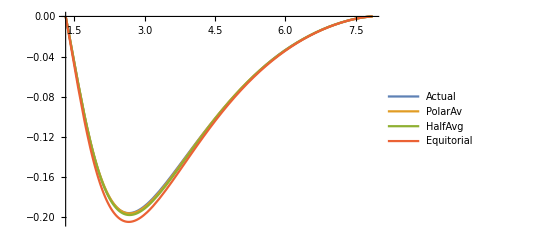

```mathematica
Plot[{RadialInFlowTrue[r],RadialInFlowPolarAvg[r],RadialInFlowHalfAvg[r],RadialInFlowEquitorial[r]},{r,RP,RI}, PlotRange->All,PlotLegends->{"Actual","PolarAv","HalfAvg","Equitorial"}]
```

#### Errors

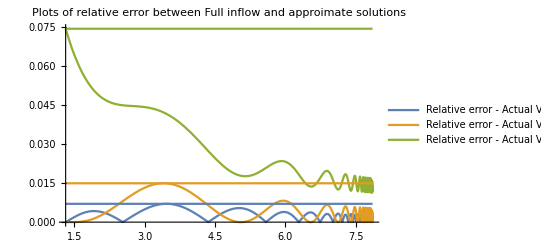

```mathematica
Q1 = Plot[{Abs[(RadialInFlowTrue[r] - RadialInFlowPolarAvg[r])/RadialInFlowTrue[r]] ,Abs[(RadialInFlowTrue[r] - RadialInFlowHalfAvg[r])/RadialInFlowTrue[r]],Abs[(RadialInFlowTrue[r] - RadialInFlowEquitorial[r])/RadialInFlowTrue[r]] },{r,RP,RI-0.001}, PlotRange->All, PlotLabel->"Plots of relative error between Full inflow and approimate solutions",PlotLegends->{"Relative error - Actual Vs PolarAv","Relative error - Actual Vs HalfAvg","Relative error - Actual Vs Equitorial"}];

Max1 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max2 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max3 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowEquitorial[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];

Q2 =ParametricPlot[{ {r,Max1},{r,Max2},{r,Max3}},{r,RP,RI}];


Show[Q1,Q2]
```

```mathematica
KerrGeoISSO[0.009,1]
```

5.97057

### MODULEFORM

#### PolarAvgFunc

```mathematica
ErrorModuleFlowPolarAvg[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowPolarAvg[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )+(Z2^2 ϵ)/J(1-a^2 J/Z2^2 - EllipticE[KZ]/EllipticK[KZ]));
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### HalfAvg

```mathematica
ErrorModuleFlowHalfAvg[a_,θINC_]:=Module[{param, ϵ, RI ,N=100,, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### Equitorial

```mathematica
ErrorModuleFlowEquitorial[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r -(a^2 Q)/((1-ϵ^2)RI^3))])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L)-a^2 ϵ);;
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] -RadialInFlowEquitorial[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### The matrices

```mathematica
<<KerrGeodesics`
n = 20;

a = Table[i, {i,0.01,0.99,0.999/n}];
 θINC =Table[i, {i,0,π,π/(2n)}];

f[x_,y_]:= {x,y}

aMatrixFunc[x_] :=x[[1]];
 aMF=Map[aMatrixFunc,Outer[f,a,  θINC ],{2}];

θMatrixFunc[x_] :=x[[2]];
 θMF=Map[θMatrixFunc,Outer[f,a,  θINC  ],{2}];

ErrorPolarAvgFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowPolarAvg[x[[1]],x[[2]]]};
ErrorPolarAvgMF = Map[ErrorPolarAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorHalfAvgFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowHalfAvg[x[[1]],x[[2]]]};
ErrorHalfAvgMF = Map[ErrorHalfAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorEquatorFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowEquitorial[x[[1]],x[[2]]]};
ErrorEquatorMF = Map[ErrorEquatorFunction,Outer[f,a,  θINC  ],{2}];
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

#### Trash

```mathematica
ϵMatrixFunc[x_] :=KerrGeoEnergy[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 ϵMF=Map[ϵMatrixFunc,Outer[f,a, χINC ],{2}];

LMatrixFunc[x_] :=KerrGeoAngularMomentum[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 LMF=Map[LMatrixFunc,Outer[f,a, χINC ],{2}];

QMatrixFunc[x_] :=KerrGeoCarterConstant[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 QMF=Map[QMatrixFunc,Outer[f,a, χINC ],{2}];

RIMatrixFunc[x_] := KerrGeoISSO[x[[1]],x[[2]]];
 RIMF=Map[RIMatrixFunc,Outer[f,a, χINC ],{2}];


RPMF = 1+Sqrt[1-aMF^2];
RMMF = 1-Sqrt[1-aMF^2];

R4 =(a^2 QMF)/((1-ϵMF^2)*RIMF^3) ;


Z1MF= Sqrt[1/2 (1+(LMF^2+QMF)/(aMF^2  (1-ϵMF^2))-Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2  (1-ϵMF^2))])];

Z2MF= Sqrt[ (aMF^2 (1-ϵMF^2))/2 (1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2))+Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2 (1-ϵMF^2))])];

KZMF = aMF^2*(1-ϵMF^2)(Z1MF^2/Z2MF^2);


rn = 10;
rValuesFunction[x_] := Table[i, {i,(1+Sqrt[1-x[[1]]^2]),KerrGeoISSO[x[[1]],x[[2]]], (KerrGeoISSO[x[[1]],x[[2]]]-(1+Sqrt[1-x[[1]]^2]))/rn}]
rMF=Map[rValuesFunction,Outer[f,a, χINC ],{2}];
```

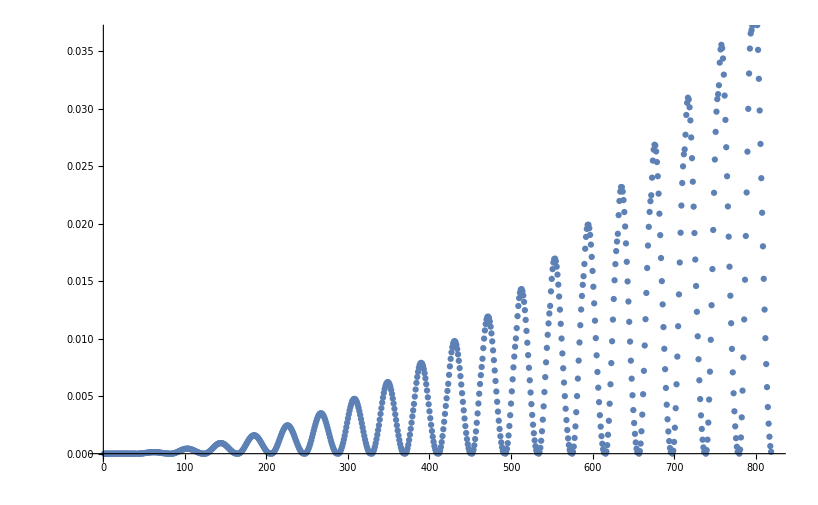

```mathematica
ListPlot[N[Flatten [ErrorEquatorMF,1]][[;;,3]]]
```

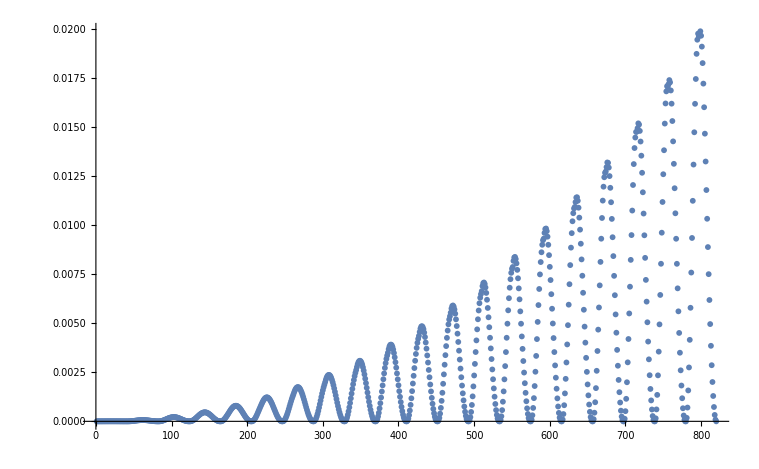

```mathematica
ListPlot[N[Flatten [ErrorPolarAvgMF,1]][[;;,3]]]
```

### ContourPlotOverParamaterSpace

```mathematica
EllipticPi[n,2π,m]
```

4 EllipticPi[n,m]

```mathematica
range
```

{-11,11}

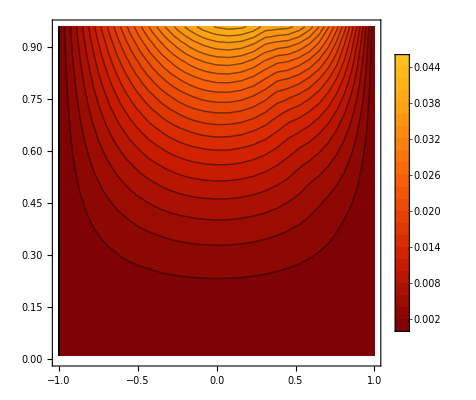
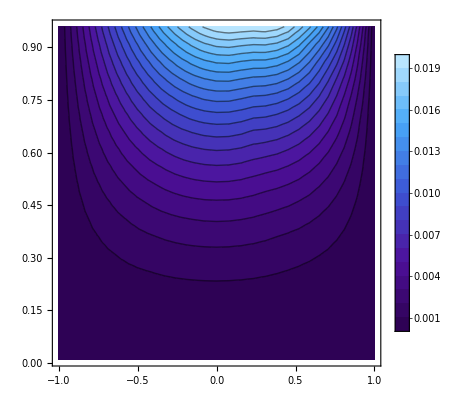

ContourFLows.pdf

```mathematica
range={0,0.5};
c1=ListContourPlot[Flatten[ErrorEquatorMF,1],PlotLegends->Automatic,FrameLabel->{MaTeX["x_{inc}",FontSize->16],MaTeX["a",FontSize->16]},ImageSize->400,PlotRange->{0,0.045},Contours->Table[i,{i,0,0.045,0.002}],ColorFunction->ColorData[{"SolarColors",{0,0.05}}],ColorFunctionScaling->False,PlotLabel->MaTeX["\\text{Max Relative Error of Equitorial Vs True Flow}",FontSize->16]];

(*c1=ListContourPlot[Flatten[ErrorEquatorMF,1],PlotLegends->Automatic,ImageSize->400,Contours->2Table[i,{i,0,0.04,0.001}],ColorFunction->ColorData[{"SolarColors",{0,0.04}}],ColorFunctionScaling->False, PlotLabel->MaTeX["\\text{Max Relative Error of Equitorial Vs True Flow}",FontSize->16],FrameLabel->{MaTeX["x_{inc}",FontSize->16],MaTeX["a",FontSize->16]}];*)

c2=ListContourPlot[Flatten[ErrorPolarAvgMF,1],PlotLegends->Automatic,ImageSize->400,Contours->2Table[i,{i,0,0.02,0.0005}],ColorFunction->ColorData[{"DeepSeaColors",{0,0.02}}],ColorFunctionScaling->False, PlotLabel->MaTeX["\\text{Max Relative Error of Polar Averaged Vs True Flow}",FontSize->16],FrameLabel->{MaTeX["x_{inc}",FontSize->16],MaTeX["a",FontSize->16]}];
pp = Row[{c1,c2}]


Export["ContourFLows.pdf",Style[pp,LineBreakWithin->False],"PDF"]
```

## Testing Solutions

```mathematica
r[2]
```

0.672257+0. ⅈ

```mathematica
a = 0.95
```

0.95

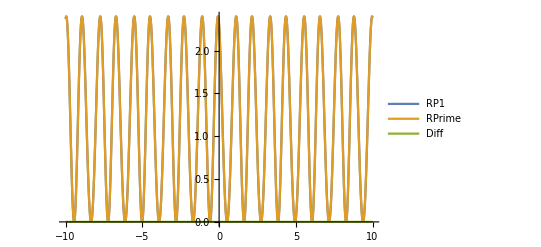

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

Plot[{Re[RPoly1[r[λ]]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly1[r[λ]]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->All,PlotRange->{{-10,10},{-0.0001,0.0001}}]
```

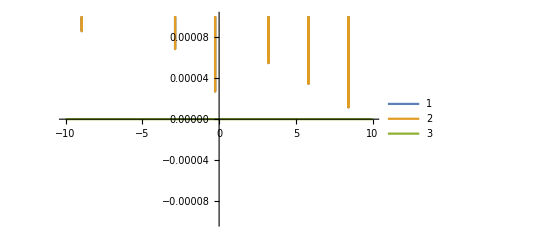

0.574236

0.484138

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},PlotRange->{{-10,10},{-0.0001,0.0001}}]
```

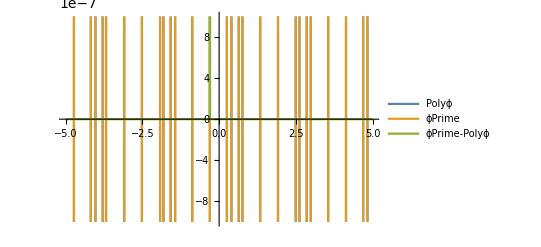

0.678752+1.32852×10^-15 ⅈ

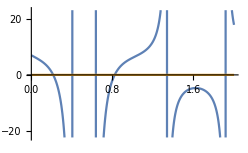

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},PlotRange->{{-5,5},{-0.000001,0.000001}}]
ϕ'[3]
```

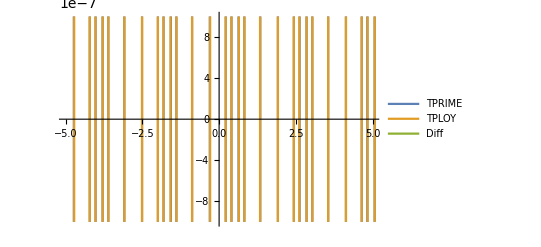

```mathematica
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{t'[λ], TPoly[λ] ,t'[λ]- TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},PlotRange->{{-5,5},{-0.000001,0.000001}}]
```

<|Λ_(r_+)^+→-1.5782+0. ⅈ,Λ_(r_-)^+→-0.876248+0. ⅈ,Λ_(r_-)^-→-0.29804+0. ⅈ,Λ_(r_+)^-→0.403913+0. ⅈ|>

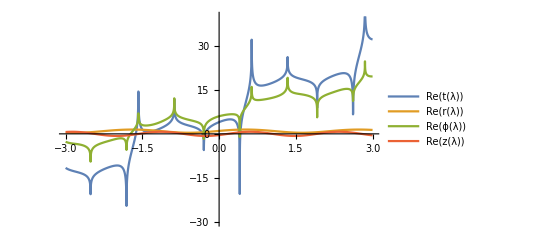

```mathematica
orbit["HorizonCrossingTimeMino"]
ee = 0.0001;
dd = 0.4036946674340016;
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[z[λ]]},{λ,-3,3},PlotLegends->"Expressions", PlotRange->{{-3,3},{-30,40}}]
```